# Real Analysis, Lecture #8

## Two Options for Exam 1: next Wednesday, covering just through the end of Chapter 2, or next Friday, covering through Section 3.1

```mathematica
a[n_]:=(1+1/n)^n
```

```mathematica
Manipulate[N[a[n],100],{n,1,1000,1}]
```

```mathematica
Limit[a[n],n->∞]
```

## Convergent Sequences whose terms all lie in a closed interval [a, b] will have a limit in that closed interval

## A Monotone Sequence Converges iff it is Bounded

## An Eventually Monotone Sequence Converges iff it is Bounded

## Cauchy Sequences and the Cauchy Convergence Criterion

```mathematica
∑_(k=1)^∞ 1/k^2
```

π^2/6

```mathematica
∑_(k=1)^∞ 1/k^100
```

(189196075638244250590454866138987443745405683066133872266771392408622790830394495422 π^100)/9815205420757514710108178059369553458327392260750404049930407987933582359080767225644716670683512153512547802166033089160919189453125

```mathematica
∑_(k=1)^∞ 1/k^3
```

Zeta[3]

```mathematica
∑_(k=1)^∞ 1/k^5
```

Zeta[5]

```mathematica
Zeta[5]//N
```

1.03693

```mathematica
∑_(k=1)^∞ 1/k^1
```

Sum::div: Sum does not converge.

∑_(k=1)^∞ 1/k

## Subsequences and the Bolzano-Weierstrass Theorem (which follows from the proof of the non-trivial fact that every sequence of real numbers has a monotone subsequence)

## A Counter-Intuitive Example

### A Simple-Looking Recusively Defined Sequence

Define a sequence x_0,x_1,x_2,x_3,… by letting x_0=.1 and letting x_n=4 x_(n-1)-4 x_(n-1)^2 for integers n≥1.  What is the behavior of this sequence as n gets larger and larger?

```mathematica
f[x_]:=4x-4x^2;
```

```mathematica
NestList[f,.1,100]
```

```mathematica
Manipulate[ListPlot[Transpose[{NestList[f,.1,b],Table[0,{k,0,b}]}],PlotStyle->{Red,PointSize[.02]},PlotRange->{{0,1},{-1,1}},Ticks->{{0,.2,.4,.6,.8,1}, },Axes->{True,False}],{b,0,50,1}]
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{Table[k,{k,0,b}],NestList[f,.1,b]}],Joined->True],ListPlot[Transpose[{Table[k,{k,0,b}],NestList[f,.1,b]}],PlotStyle->{Red,PointSize[.025]}],PlotRange->{{0,50},{0,1}},AxesLabel->{"n","x_n"}],{b,0,50,1}]
```

This is an example of "chaos".  Certain statistical/probabilistic patterns are evident, however.

```mathematica
Histogram[NestList[f,.1,100000],AxesLabel->{"x_n","frequency"}]
```

An area of math called Ergodic theory is where the probabilistic patterns in these deterministic situations is studied.

## Cobweb Plots

```mathematica
CobWebPlot[f_,{x_,xmin_,xmax_},{y_,ymin_,ymax_},seed_,iterates_]:=
	Module[{myList},
		myList=NestList[f,seed,iterates]//N;
		Plot[{f[x],x},{x,xmin,xmax},PlotStyle->{{Thick,Red},{Thick,Blue}},Epilog->Map[{Thick,Line[{{#,#},{#,f[#]},{f[#],f[#]}}]}&,myList],
	PlotRange->{ymin,ymax},AspectRatio->1]]
```

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Manipulate[CobWebPlot[Subscript[f, μ],{x,0,1},{y,0,1},.1,n],{μ,.1,4},{n,0,25,1},LabelStyle->Large]
```

```mathematica
f[x_]:=(x/2)+(3/x);Manipulate[CobWebPlot[f,{x,2,4},{y,2,4},3,n],{n,0,10,1},LabelStyle->Large]
```

## Density: Both the set of rational numbers and the set of irrational numbers are dense in ℝ

A set A⊆ℝ is said to be dense in ℝ if, for any point x∈ℝ and any ϵ>0, there exists a y∈A with y≠x such that y∈(x-ϵ,x+ϵ)  (that is, A∩(x-ϵ,x+ϵ)≠∅ for all x∈ℝ and for all ϵ>0).  Theorem 1.18 essentially says that both ℚ and ℝ\ℚ are dense in ℝ.  (Think about this!)

An intuitive way to imagine this is to imagine that the rationals and irrationals are "everywhere" (without being every point) on the real number line.

## Limsups and Liminfs

```mathematica
a[n_]:=n/3-Floor[n/3]
```

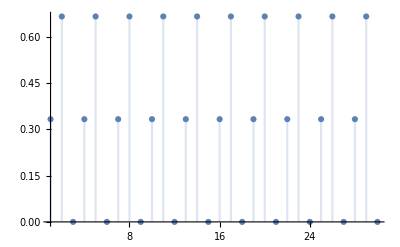

```mathematica
DiscretePlot[a[n],{n,1,30}]
```

```mathematica
a[n_]:=(-1)^(n)*(1+1/n)
```

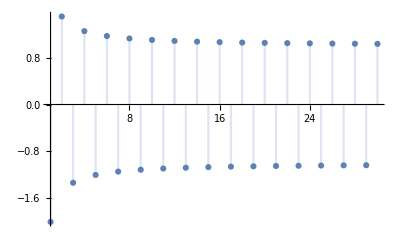

```mathematica
DiscretePlot[a[n],{n,1,30}]
```

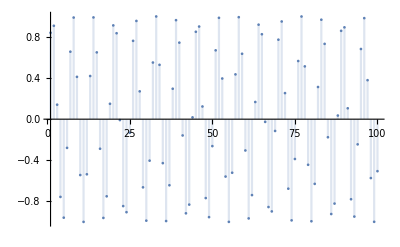

```mathematica
a[n_]:=Sin[n];DiscretePlot[a[n],{n,1,100}]
```

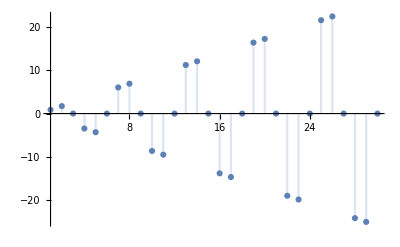

```mathematica
a[n_]:=n*Sin[n*π/3];DiscretePlot[a[n],{n,1,30}]
```

```mathematica
DiscretePlot[a[n],{n,1,30}]
```

## What are Limsups and Liminfs good for?

### Does ∑ _(k=1)^∞ (2+(-1)^k)*2^-k=1/2+3/4+1/8+3/16+1/32+3/64+··· converge?

```mathematica
a[k_]:=(2+(-1)^(k))*2^(-k)
```

```mathematica
DiscretePlot[a[k],{k,1,20},PlotRange->{0,.8},PlotStyle->Red]
```

```mathematica
∑_(k=1)^∞ a[k]
```

5/3

### Can this be proved? With the Ratio Test? With the Root Test?

```mathematica
DiscretePlot[a[k+1]/a[k],{k,1,20},PlotRange->{0,2},PlotStyle->Red]
```

```mathematica
DiscretePlot[a[k]^(1/k),{k,1,20},PlotRange->{0,1},PlotStyle->Red]
```